# Spike Parser

## Setup (automatically initialized when this notebook is opened)

### Load Combinatorica package

In order to use BinarySearch capabilities, the Combinatorica Package is necessary.

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

### Function definitions

#### OrganizeRefData[fileName_, timeBounds_, regionBounds_]

This function takes the filename of a spike file and parses it for the important data.  It also takes the timeBounds and regionBounds variables as input.  timeBounds is a variable that defines the start and stop times between which the data is considered valid.  regionBounds is a similar variable, except that it defines the valid locations for the neuron’s x,y coordinate.

As output, this function returns a single data member which is organized as {I_l,I_ref,{{x,y},f_avg}} where each I_l, I_ref value has a corresponding matrix of the firing rates per neuron.

```mathematica
OrganizeRefData[fileName_,timeBounds_,regionBounds_]:=Module[{m,dataInput,collapsedData,spikeTimes,neurons,avgFiringRate,tempParams,tempIref, tempIl},
tempParams=StringCases[fileName,"somaCalibRef_Iref_"~~Iref:NumberString~~"_Il_"~~Il:NumberString~~".spk"->{Iref,Il}];
tempIref=ToExpression[tempParams⟦1,1⟧];
tempIl=ToExpression[tempParams⟦1,2⟧];

Irefs=Union[Append[Irefs,tempIref]];
Ils= Union[Append[Ils,tempIl]];

m = BinaryReadList[fileName,{"UnsignedInteger16","UnsignedInteger16","UnsignedInteger16","Real64"}];
dataInput=Transpose[Drop[Transpose[m], 1]];  (*Print["Drop first column: "];*)
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦3⟧,timeBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦3⟧,timeBounds⟦2⟧]]}];  (*Print["Filter for valid spike times: "];*)
dataInput=Sort[dataInput];
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦1⟧,regionBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦1⟧,regionBounds⟦2⟧]]}];  (*Print["Filter for valid neuron addresses based on x: "];*)
dataInput = SortBy[dataInput,#⟦2⟧&];
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦2⟧,regionBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦2⟧,regionBounds⟦2⟧]]}];(*Print["Filter for valid neuron addresses based on y: "];*)
dataInput=Sort[dataInput];
(*Filtering the data is still a somewhat slow operation; almost 2 seconds per data file*)

collapsedData=GatherBy[dataInput,{#⟦{1,2}⟧}&];  (*Print["Gather data by coordinates: "];*)
spikeTimes =List/@( Transpose[#]⟦3⟧&/@collapsedData);  (*Print["Collect spike times: "];*)
neurons = List/@(Drop[Flatten[Take[#,1]],-1]&/@collapsedData);  (*Print["Collect neuron coordinates: "];*)
avgFiringRate=List/@(Length[Delete[#,0]]/(Plus@@(timeBounds/1000))&/@spikeTimes);
(*dataInput=Join[neurons,spikeTimes,2];
dataInput=Join[dataInput,avgFiringRate,2];*)  (*The previous two lines are commented out in order to minimize the memory profile by not keeping the spiketimes, after the avg firing rate is calculated *)
dataInput=Join[neurons,avgFiringRate,2];
dataInput={tempIl, tempIref,dataInput[[1;;3]]}; (* Use this when you want to save the first 3 neurons *)
(*dataInput={tempIl, tempIref,dataInput};*)
Return[dataInput];
](* OrganizeRefData Module *)
```

#### OrganizeFGData[fileName_,timeBounds_]

This function takes the filename of a spike file and parses it for the important data.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data is considered valid.   There is an overloaded method that also takes regionBounds as an input option and filters out any x and y coordinates that aren’t within the region specified by regionBounds.  (This overloaded function has a minor bug at the moment where it isn’t able to Join two empty lists, which occurs when the region filtering process filters out all x and y coordinates for a given g_sat and/or e_rev setting).

As output, this function returns a single data member which is organized as {g_sat,e_rev,{{x,y},f_avg}} where each g_sat, e_rev value has a corresponding matrix of the firing rates per neuron.

```mathematica
OrganizeFGData[fileName_,timeBounds_]:=Module[{m,dataInput,collapsedData,spikeTimes,neurons,avgFiringRate,tempParams,tempErev, tempGsat},
tempParams=StringCases[fileName,"syn_results_FG_erev"~~erev:NumberString~~"_gmax"~~gsat:NumberString~~".spk"->{erev,gsat}];
tempErev=ToExpression[tempParams⟦1,1⟧];
tempGsat=ToExpression[tempParams⟦1,2⟧];

erevs=Union[Append[erevs,tempErev]];
gsats= Union[Append[gsats,tempGsat]];

m = BinaryReadList[fileName,{"UnsignedInteger16","UnsignedInteger16","UnsignedInteger16","Real64"}];
dataInput=Transpose[Drop[Transpose[m], 1]];  (*Print["Drop first column: "];*)
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦3⟧,timeBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦3⟧,timeBounds⟦2⟧]]}];  (*Print["Filter for valid spike times: "];*)
dataInput=Sort[dataInput];

collapsedData=GatherBy[dataInput,{#⟦{1,2}⟧}&];  (*Print["Gather data by coordinates: "];*)
spikeTimes =List/@( Transpose[#]⟦3⟧&/@collapsedData);  (*Print["Collect spike times: "];*)
neurons = List/@(Drop[Flatten[Take[#,1]],-1]&/@collapsedData);  (*Print["Collect neuron coordinates: "];*)
avgFiringRate=List/@(Length[Delete[#,0]]/(Plus@@(timeBounds/1000))&/@spikeTimes);
dataInput=Join[neurons,spikeTimes,2];
dataInput=Join[dataInput,avgFiringRate,2];
(*dataInput={tempErev, tempGsat,dataInput[[1;;3]]}; Use this when you want to save the first 3 neurons *)
dataInput={tempErev, tempGsat,dataInput};
Return[dataInput];
](* OrganizeFGData Module *)

OrganizeFGData[fileName_,timeBounds_, regionBounds_]:=Module[{m,dataInput,collapsedData,spikeTimes,neurons,avgFiringRate,tempParams,tempErev, tempGsat},
tempParams=StringCases[fileName,"syn_results_FG_erev"~~erev:NumberString~~"_gmax"~~gsat:NumberString~~".spk"->{erev,gsat}];
tempErev=ToExpression[tempParams⟦1,1⟧];
tempGsat=ToExpression[tempParams⟦1,2⟧];

erevs=Union[Append[erevs,tempErev]];
gsats= Union[Append[gsats,tempGsat]];

m = BinaryReadList[fileName,{"UnsignedInteger16","UnsignedInteger16","UnsignedInteger16","Real64"}];
dataInput=Transpose[Drop[Transpose[m], 1]];  (*Print["Drop first column: "];*)
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦3⟧,timeBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦3⟧,timeBounds⟦2⟧]]}];  (*Print["Filter for valid spike times: "];*)
dataInput=Sort[dataInput];
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦1⟧,regionBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦1⟧,regionBounds⟦2⟧]]}];  (*Print["Filter for valid neuron addresses based on x: "];*)
dataInput = SortBy[dataInput,#⟦2⟧&];
dataInput=Take[dataInput,{Ceiling[BinarySearch[Transpose[dataInput]⟦2⟧,regionBounds⟦1⟧]],Floor[BinarySearch[Transpose[dataInput]⟦2⟧,regionBounds⟦2⟧]]}];(*Print["Filter for valid neuron addresses based on y: "];*)
dataInput=Sort[dataInput];
(*Filtering the data is still a somewhat slow operation; almost 2 seconds per data file*)

collapsedData=GatherBy[dataInput,{#⟦{1,2}⟧}&];  (*Print["Gather data by coordinates: "];*)
spikeTimes =List/@( Transpose[#]⟦3⟧&/@collapsedData);  (*Print["Collect spike times: "];*)
neurons = List/@(Drop[Flatten[Take[#,1]],-1]&/@collapsedData);  (*Print["Collect neuron coordinates: "];*)
avgFiringRate=List/@(Length[Delete[#,0]]/(Plus@@(timeBounds/1000))&/@spikeTimes);
dataInput=Join[neurons,avgFiringRate,2];
(*dataInput={tempGsat, tempErev,dataInput[[1;;3]]}; Use this when you only want to save the first 3 neurons *)
dataInput={tempErev, tempGsat,dataInput};
Return[dataInput];
](* OrganizeFGData Module *)
```

#### GetRefPlotData[data_,x_,y_]

This function is used to get the refractory period plot data for any given coordinate.  As input, it takes the data structure that is setup using the OrganizeRefData method, and an (x, y) coordinate.  Note: This function is overloaded to accept either individual x and y coordinates or a list form of an {x,y} coordinate.

```mathematica
GetRefPlotData[data_,x_,y_]:=Module[{neuronIndex,xyCoord},
neuronIndex=Flatten[Position[#,{x,y}]&/@Union[data⟦All,3,All,1⟧]];
xyCoord =Transpose[{1./data⟦All,2⟧,1./#&/@data⟦All,3,neuronIndex⟦1⟧,2⟧}];
Return[xyCoord];
](* Module *)
GetRefPlotData[data_,coord_]:=Module[{neuronIndex,xyCoord},
neuronIndex=Flatten[Position[#,coord]&/@Union[data⟦All,3,All,1⟧]];
xyCoord =Transpose[{1./data⟦All,2⟧,1./#&/@data⟦All,3,neuronIndex⟦1⟧,2⟧}];
Return[xyCoord];
](* Module *)
```

#### GetFGPlotData[data_,x_,y_]

This function is used to get the refractory period plot data for any given coordinate.  As input, it takes the data structure that is setup using the OrganizeFGData method, and an (x, y) coordinate.  Note: This function is overloaded to accept either individual x and y coordinates or a list form of an {x,y} coordinate.

```mathematica
GetFGPlotData[data_,x_,y_]:=Module[{neuronIndices,validCondition,xyCoord,tempIndices},
neuronIndices=Transpose[Drop[Transpose[Position[data,{x,y}]],-1]];
xyCoord ={data⟦#⟦1⟧,1⟧,data⟦#⟦1⟧,2⟧,data⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧}&/@neuronIndices;
xyCoord=GatherBy[xyCoord,#⟦1⟧&];
Return[xyCoord];
](* Module *)
GetFGPlotData[data_,coord_]:=Module[{neuronIndices,validCondition,xyCoord,tempIndices},
neuronIndices=Transpose[Drop[Transpose[Position[data,coord]],-1]];
xyCoord ={data⟦#⟦1⟧,1⟧,data⟦#⟦1⟧,2⟧,data⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧}&/@neuronIndices;
xyCoord=GatherBy[xyCoord,#⟦1⟧&];
Return[xyCoord];
](* Module *)
```

### Set working directory to the location of *.spk data files

```mathematica
workingDir=SystemDialogInput["Directory","C:\\Users\\noza\\Google Drive\\Work\\Mathematica\\CalibrationManipulator\\data\\run1.4", WindowTitle->"Select spike (*.spk) data directory"];
(*SetDirectory["C:\\Users\\noza\\Google Drive\\Work\\Mathematica\\CalibrationManipulator\\data\\run1.4\\refData"];*)
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]]
```

SetDirectory::fstr: File specification TraditionalForm`$Canceled is not a string of one or more characters.

Working Directory:  C:\Users\noza\Documents

### Load all *.spk filenames into local variable

```mathematica
filesInDir =FileNames["*.spk"];
Print[Style["Number of spike files:  ", FontFamily->"Helvetica", Bold],Length[filesInDir]];
Print[Style["Sample of filenames in pwd: ", FontFamily->"Helvetica", Bold],RandomSample[filesInDir,4]];
```

Number of spike files:  0

RandomSample::smplen: RandomSample cannot generate a sample of length TraditionalForm`4, which is greater than the length of the sample set TraditionalForm`{}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

Sample of filenames in pwd: RandomSample[{},4]

## Information Processing (Run-time)

### Process Ref data from each file in filesInDir

```mathematica
regionBounds={95.5,159.5};
timeBounds ={499.975,1500.025};
Irefs=.; Ils=.;refData=.;Irefs={};Ils={};
AbsoluteTiming[
refData=OrganizeRefData[#, timeBounds,regionBounds]&/@filesInDir;
refData=SortBy[refData,#⟦2⟧&];
]
```

{69.935,Null}

### Process FG data from each file in filesInDir

```mathematica
regionBounds={95.5,159.5};
timeBounds ={299.975,1700.025};
erevs=.; gsats=.;data=.;erevs={};gsats={};
AbsoluteTiming[
data=OrganizeFGData[#, timeBounds]&/@filesInDir;
data=SortBy[data,#⟦1⟧&];
(*data=GatherBy[data,#⟦1⟧&];*)
]
```

{11.2944,Null}

```mathematica
data[#⟦1⟧,#⟦2⟧,#⟦3⟧]&/@Transpose[Drop[Transpose[Position[data,{112,120}]],-1]]⟦1;;3⟧
```

{(«1»)(4,3,16),(«1»)(5,3,16),(«1»)(6,3,16)}

Get all of the neuron coordinates by any e_rev,g_sat setting.  The index value sets which e_rev,g_sat value should be taken.

```mathematica
neuronCoords = data⟦All,3,All,1⟧
```

```mathematica
fgPlotData=GetFGPlotData[data,112,120]
```

{(3.415 | 0.28 | 19.
3.415 | 0.37 | 30.5
3.415 | 0.47 | 38.
3.415 | 0.56 | 45.5
3.415 | 0.65 | 49.5
3.415 | 0.74 | 53.
3.415 | 0.84 | 56.
3.415 | 0.93 | 58.5
3.415 | 1.02 | 60.
3.415 | 1.11 | 61.5
3.415 | 1.2 | 63.5
3.415 | 1.3 | 65.5
3.415 | 1.39 | 66.
3.415 | 1.48 | 67.
3.415 | 1.57 | 68.
3.415 | 1.67 | 68.5
3.415 | 1.76 | 69.5
3.415 | 1.85 | 69.5
3.415 | 1.94 | 70.
3.415 | 2.03 | 70.5
3.415 | 2.13 | 71.
3.415 | 2.22 | 70.5
3.415 | 2.31 | 70.5
3.415 | 2.4 | 70.5
3.415 | 2.5 | 70.5
3.415 | 2.59 | 70.
3.415 | 2.68 | 69.5
3.415 | 2.77 | 69.5
3.415 | 2.87 | 69.
3.415 | 2.96 | 68.
3.415 | 3.05 | 68.
3.415 | 3.14 | 67.
3.415 | 3.23 | 66.5
3.415 | 3.33 | 64.5
3.415 | 3.42 | 63.
3.415 | 3.51 | 61.5
3.415 | 3.6 | 60.5
3.415 | 3.79 | 56.
3.415 | 3.88 | 54.
3.415 | 3.97 | 52.
3.415 | 4.06 | 51.5
3.415 | 4.16 | 48.5
3.415 | 4.25 | 44.5
3.415 | 4.34 | 41.5
3.415 | 4.43 | 33.5
3.415 | 4.53 | 25.5
3.415 | 4.62 | 6.
3.415 | 4.71 | 9.5),(5. | 0.16 | 25.
5. | 0.32 | 50.
5. | 0.48 | 64.
5. | 0.63 | 71.5
5. | 0.79 | 78.
5. | 0.95 | 83.
5. | 1.11 | 86.5
5. | 1.26 | 89.5
5. | 1.42 | 93.
5. | 1.58 | 95.
5. | 1.74 | 97.5
5. | 1.89 | 98.5
5. | 2.05 | 100.
5. | 2.21 | 101.5
5. | 2.37 | 102.
5. | 2.52 | 103.5
5. | 2.68 | 104.
5. | 2.84 | 105.
5. | 3. | 105.5
5. | 3.15 | 105.5
5. | 3.31 | 106.
5. | 3.47 | 106.
5. | 3.63 | 106.5
5. | 3.78 | 106.
5. | 3.94 | 106.
5. | 4.1 | 105.5
5. | 4.26 | 105.
5. | 4.41 | 104.5
5. | 4.57 | 104.
5. | 4.73 | 103.
5. | 4.89 | 102.
5. | 5.04 | 101.
5. | 5.2 | 100.
5. | 5.36 | 98.5
5. | 5.52 | 97.
5. | 5.67 | 95.5
5. | 5.83 | 93.5
5. | 5.99 | 92.
5. | 6.15 | 90.
5. | 6.46 | 84.
5. | 6.62 | 81.
5. | 6.78 | 76.5
5. | 6.93 | 72.
5. | 7.09 | 64.5
5. | 7.25 | 56.5
5. | 7.41 | 42.5
5. | 7.56 | 41.
5. | 7.72 | 12.),(7. | 0.24 | 60.5
7. | 0.48 | 83.
7. | 0.72 | 94.5
7. | 0.96 | 103.
7. | 1.2 | 108.
7. | 1.43 | 113.
7. | 1.67 | 117.
7. | 1.91 | 120.
7. | 2.15 | 122.5
7. | 2.39 | 125.
7. | 2.63 | 126.5
7. | 2.86 | 128.5
7. | 3.1 | 129.5
7. | 3.34 | 131.
7. | 3.58 | 132.
7. | 3.82 | 133.
7. | 4.06 | 133.5
7. | 4.29 | 134.
7. | 4.53 | 134.5
7. | 4.77 | 134.5
7. | 5.01 | 134.5
7. | 5.25 | 135.
7. | 5.49 | 134.5
7. | 5.72 | 134.5
7. | 5.96 | 134.
7. | 6.2 | 133.5
7. | 6.44 | 132.5
7. | 6.68 | 132.5
7. | 6.92 | 131.
7. | 7.15 | 130.5
7. | 7.39 | 129.5
7. | 7.63 | 128.
7. | 7.87 | 126.5
7. | 8.11 | 125.
7. | 8.35 | 123.5
7. | 8.58 | 121.5
7. | 8.82 | 117.
7. | 9.06 | 115.
7. | 9.3 | 111.
7. | 9.78 | 102.5
7. | 10.01 | 97.
7. | 10.25 | 90.
7. | 10.49 | 82.
7. | 10.73 | 81.5
7. | 10.97 | 66.5
7. | 11.21 | 35.)}

```mathematica
Union[Flatten[fgPlotData[[All,All,1]]]]
```

{3.415,5.,7.}

#### Plot Data

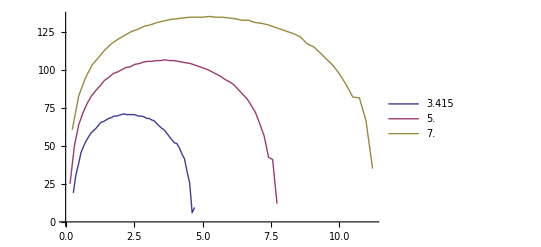

```mathematica
ListLinePlot[Transpose[Drop[Transpose[#],1]]&/@fgPlotData,PlotLegends->Union[Flatten[fgPlotData[[All,All,1]]]]]
```

```mathematica
data1=GatherBy[data,#⟦1⟧&];
```

```mathematica
data1
```

```mathematica
neuronIndices=Transpose[Drop[Transpose[Position[data,{112,120}]],-1]];
xyCoord ={data⟦#⟦1⟧,1⟧,data⟦#⟦1⟧,2⟧,data⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧}&/@neuronIndices;
xyCoord=GatherBy[xyCoord,#⟦1⟧&];
```

```mathematica
xyCoord[[All,All]]
```

{(3.415 | 0.28 | 19.
3.415 | 0.37 | 30.5
3.415 | 0.47 | 38.
3.415 | 0.56 | 45.5
3.415 | 0.65 | 49.5
3.415 | 0.74 | 53.
3.415 | 0.84 | 56.
3.415 | 0.93 | 58.5
3.415 | 1.02 | 60.
3.415 | 1.11 | 61.5
3.415 | 1.2 | 63.5
3.415 | 1.3 | 65.5
3.415 | 1.39 | 66.
3.415 | 1.48 | 67.
3.415 | 1.57 | 68.
3.415 | 1.67 | 68.5
3.415 | 1.76 | 69.5
3.415 | 1.85 | 69.5
3.415 | 1.94 | 70.
3.415 | 2.03 | 70.5
3.415 | 2.13 | 71.
3.415 | 2.22 | 70.5
3.415 | 2.31 | 70.5
3.415 | 2.4 | 70.5
3.415 | 2.5 | 70.5
3.415 | 2.59 | 70.
3.415 | 2.68 | 69.5
3.415 | 2.77 | 69.5
3.415 | 2.87 | 69.
3.415 | 2.96 | 68.
3.415 | 3.05 | 68.
3.415 | 3.14 | 67.
3.415 | 3.23 | 66.5
3.415 | 3.33 | 64.5
3.415 | 3.42 | 63.
3.415 | 3.51 | 61.5
3.415 | 3.6 | 60.5
3.415 | 3.79 | 56.
3.415 | 3.88 | 54.
3.415 | 3.97 | 52.
3.415 | 4.06 | 51.5
3.415 | 4.16 | 48.5
3.415 | 4.25 | 44.5
3.415 | 4.34 | 41.5
3.415 | 4.43 | 33.5
3.415 | 4.53 | 25.5
3.415 | 4.62 | 6.
3.415 | 4.71 | 9.5),(5. | 0.16 | 25.
5. | 0.32 | 50.
5. | 0.48 | 64.
5. | 0.63 | 71.5
5. | 0.79 | 78.
5. | 0.95 | 83.
5. | 1.11 | 86.5
5. | 1.26 | 89.5
5. | 1.42 | 93.
5. | 1.58 | 95.
5. | 1.74 | 97.5
5. | 1.89 | 98.5
5. | 2.05 | 100.
5. | 2.21 | 101.5
5. | 2.37 | 102.
5. | 2.52 | 103.5
5. | 2.68 | 104.
5. | 2.84 | 105.
5. | 3. | 105.5
5. | 3.15 | 105.5
5. | 3.31 | 106.
5. | 3.47 | 106.
5. | 3.63 | 106.5
5. | 3.78 | 106.
5. | 3.94 | 106.
5. | 4.1 | 105.5
5. | 4.26 | 105.
5. | 4.41 | 104.5
5. | 4.57 | 104.
5. | 4.73 | 103.
5. | 4.89 | 102.
5. | 5.04 | 101.
5. | 5.2 | 100.
5. | 5.36 | 98.5
5. | 5.52 | 97.
5. | 5.67 | 95.5
5. | 5.83 | 93.5
5. | 5.99 | 92.
5. | 6.15 | 90.
5. | 6.46 | 84.
5. | 6.62 | 81.
5. | 6.78 | 76.5
5. | 6.93 | 72.
5. | 7.09 | 64.5
5. | 7.25 | 56.5
5. | 7.41 | 42.5
5. | 7.56 | 41.
5. | 7.72 | 12.),(7. | 0.24 | 60.5
7. | 0.48 | 83.
7. | 0.72 | 94.5
7. | 0.96 | 103.
7. | 1.2 | 108.
7. | 1.43 | 113.
7. | 1.67 | 117.
7. | 1.91 | 120.
7. | 2.15 | 122.5
7. | 2.39 | 125.
7. | 2.63 | 126.5
7. | 2.86 | 128.5
7. | 3.1 | 129.5
7. | 3.34 | 131.
7. | 3.58 | 132.
7. | 3.82 | 133.
7. | 4.06 | 133.5
7. | 4.29 | 134.
7. | 4.53 | 134.5
7. | 4.77 | 134.5
7. | 5.01 | 134.5
7. | 5.25 | 135.
7. | 5.49 | 134.5
7. | 5.72 | 134.5
7. | 5.96 | 134.
7. | 6.2 | 133.5
7. | 6.44 | 132.5
7. | 6.68 | 132.5
7. | 6.92 | 131.
7. | 7.15 | 130.5
7. | 7.39 | 129.5
7. | 7.63 | 128.
7. | 7.87 | 126.5
7. | 8.11 | 125.
7. | 8.35 | 123.5
7. | 8.58 | 121.5
7. | 8.82 | 117.
7. | 9.06 | 115.
7. | 9.3 | 111.
7. | 9.78 | 102.5
7. | 10.01 | 97.
7. | 10.25 | 90.
7. | 10.49 | 82.
7. | 10.73 | 81.5
7. | 10.97 | 66.5
7. | 11.21 | 35.)}

```mathematica
Union[#]&/@xyCoord[[All,All,1]]
```

(3.415
5.
7.)

```mathematica
Transpose[xyCoord[[All,All,1]]]
```

Transpose::nmtx: The first two levels of the one-dimensional list TraditionalForm`{{3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415, 3.415}, {« 1 »}, {7., 7., 7., 7., 7., 7., 7., 7., « 30 », 7., 7., 7., 7., 7., 7., 7., 7.}} cannot be transposed.

Transpose[{{3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415,3.415},{5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.},{7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.}}]

## Appendix

### Extract I_ref and I_l values from the filenames (This step is optional b/c OrganizeRefData inherently handles it as well)

```mathematica
Irefs=Sort[ToExpression[Delete[Transpose[StringCases[#,"somaCalibRef_Iref_"~~Iref:NumberString~~"_Il_"~~__~~".spk"->Iref]&/@filesInDir],0]]]
Ils=Union[Delete[Transpose[StringCases[#,"somaCalibRef_Iref_"~~__~~"_Il_"~~Il:NumberString~~".spk"->Il]&/@filesInDir],0]]
```

{1.26582,1.31579,1.36986,1.42857,1.49254,1.5625,1.63934,1.72414,1.81818,1.92308,2.04082,2.17391,2.32558,2.5,2.7027,2.94118,3.22581,3.57143,4.,4.54545,5.26316,6.25,7.69231,10.,14.2857,25.,100.}

{0.617833191318}

### Test scripts to prove that parsing the filename for Iref and Il values worked properly

```mathematica
fileName=filesInDir[[1]]
testRule = "somaCalibRef_Iref_"~~Iref:NumberString~~"_Il_"~~Il:NumberString~~".spk"->{Iref,Il}
tempParams=StringCases[fileName,testRule]
tempParams[[1,2]]//FullForm
fileName=.; testRule=.;
filName=.;
```

somaCalibRef_Iref_100.0_Il_0.617833191318.spk

somaCalibRef_Iref_~~Iref:NumberString~~_Il_~~Il:NumberString~~.spk→{Iref,Il}

(100.0 | 0.617833191318)

"0.617833191318"

### Test scripts to prove that the plot dataset can be generated for any given neuron

```mathematica
Union[data⟦All,3,All,1⟧]; (* Gather a list of the coordinates that ar valid *)
x=96;
y=98;
neuronIndex=Flatten[Position[#,{x,y}]&/@Union[data⟦All,3,All,1⟧]] (* Get the position that corresponds to a neuron's coordinate *)
1./#&/@data⟦All,3,neuronIndex⟦1⟧,2⟧ (* Calculate 1/f for each configuration *)
xyCoord =Transpose[{1./data[[All,2]],1./#&/@data⟦All,3,neuronIndex⟦1⟧,2⟧}] (* Creates a data set of the Iref plot for an individual neuron; x = 1/Iref, and y = 1/f *)
```

{3}

{0.0540541,0.0512821,0.0512821,0.0487805,0.047619,0.0465116,0.0454545,0.0434783,0.0425532,0.0408163,0.0392157,0.0377358,0.0363636,0.0350877,0.0333333,0.031746,0.030303,0.0289855,0.027027,0.0240964,0.0227273,0.0212766,0.0196078,0.0183486,0.0168067,0.0155039,0.0136054}

(0.79 | 0.0540541
0.76 | 0.0512821
0.73 | 0.0512821
0.7 | 0.0487805
0.67 | 0.047619
0.64 | 0.0465116
0.61 | 0.0454545
0.58 | 0.0434783
0.55 | 0.0425532
0.52 | 0.0408163
0.49 | 0.0392157
0.46 | 0.0377358
0.43 | 0.0363636
0.4 | 0.0350877
0.37 | 0.0333333
0.34 | 0.031746
0.31 | 0.030303
0.28 | 0.0289855
0.25 | 0.027027
0.22 | 0.0240964
0.19 | 0.0227273
0.16 | 0.0212766
0.13 | 0.0196078
0.1 | 0.0183486
0.07 | 0.0168067
0.04 | 0.0155039
0.01 | 0.0136054)